```mathematica
(*** List of points ***)
points = {{0, 3}, {1, 2}, {2, 8}}
```

```mathematica
{{0,3},{1,2},{2,8}}

(*** Plot of points - clearly not linear ***)
```

```mathematica
p1 = ListPlot[points]
```

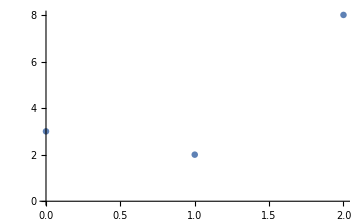
```mathematica
-Graphics-

(*** Use normal eq. to find an approximation for the inconsistent sys. ***)
```

```mathematica
Inverse[{{1, 0, 2}, {1, 1, 1}}.{{1, 1},{0,1},{2,1}}].{{1, 0, 2}, {1, 1, 1}}.{2, 3, 8}
```

```mathematica
{5/2,11/6}

(*** Use coefficient vector to find approx. vector in image of matrix ***)
```

```mathematica
{{1, 1},{0,1},{2,1}}.{{5/2},{11/6}}
```

```mathematica
{{13/3},{11/6},{41/6}} (*** these are the y values replacing [2, 3, 8] ***)
```

```mathematica
(*** m = 5/2, b = 11/6 ***)
line = {{0, 11/6}, {1, 26/6}, {2, 41/6}}
```

{{0,11/6},{1,13/3},{2,41/6}}

```mathematica
(*** Approx. Line ***)
```

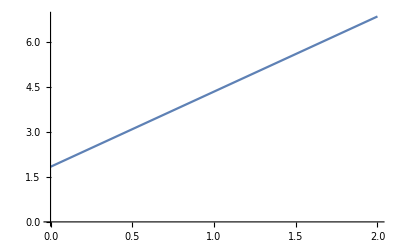

```mathematica
p2 =ListLinePlot[line]
```

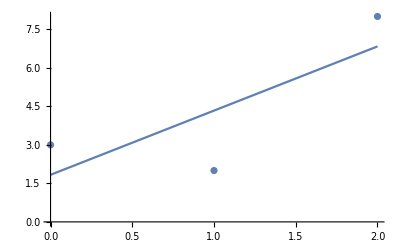

```mathematica
(*** Combine graphs. Shows plots and a best-fit line. ***)

Show[p1, p2]
```